```mathematica
f1[c_,s_,i_]:= (c-a)(1-c) - α s-β i;
```

```mathematica
f2[c_,s_,i_]:= rs(1-s)- γ c+ δ i;
```

```mathematica
f3[c_,s_,i_]:= ri( 1-i )+ η c
```

```mathematica
sol3 = Solve[f3[c,s,i]==0, c][[1,1]]
```

c→((-1+i) ri)/η

```mathematica
F1[s_,i_]:= Simplify[ f1[((-1+i) ri)/η, s, i]]
```

```mathematica
F2[s_,i_]:= Simplify[ f2[((-1+i) ri)/η, s, i]]
```

```mathematica
F11[s_,i_, α_, β_, η_, a_,ri_]:=-s α-i β+(((-1+i) ri-η) (ri-i ri+a η))/η^2
```

```mathematica
F22[s_,i_, δ_, γ_,η_,ri_,rs_]:=rs-rs s-i δ-((-1+i) ri γ)/η
```

```mathematica
Manipulate[
Show[
{VectorPlot[
{F11[s,i, α, β, η, a,ri],
F22[s,i, δ, γ,η,ri,rs]},
{s,0,2},
{i,1,2},
VectorScale->{0.06,0.4,None},
Axes->True,
VectorPoints->30,
VectorStyle->{GrayLevel[0.6]}], 
ContourPlot[
{F11[s,i, α, β, η, a,ri]==0,
F22[s,i, δ, γ,η,ri,rs]==0},
{s,0,2},
{i,1,2}]
}
],
{{ri ,0.595},0,1},
{{rs ,0.6},0,1},
{{γ,0.054},0,1},
{{δ,0.006},0,1},
{{α,0.15},0,10},
{{β,0.14},0,5},
{{a,2.28},0,10},
{{η,0.15},0.01,5}]
```

```mathematica
Manipulate[
StreamPlot[{
F11[s,i, α, β, η, a,ri],
F22[s,i, δ, γ,η,ri,rs]},
{s,-10,10},
{i,-10,15}]
,
{{ri ,0.264},0,1},
{{rs ,0.6},0,1},
{{γ,0.21},0,1},
{{δ,0.006},0,1},
{{α,0.15},0,10},
{{β,0.14},0,5},
{{a,3.21},0,10},
{{η,0.15},0.01,5}]
```

```mathematica
f11[c_,s_,i_, a_, α_, β_]:= c(c-a)(1-c) - α c s-β c i;
```

```mathematica
f22[c_,s_,i_, rs_, γ_, δ_]:= rs s(1-s)- γ s c- δ s i;
```

```mathematica
f33[c_,i_, ri_, η_]:= ri i( 1-i )+ η i c;
```

```mathematica
Manipulate[
StreamPlot3D[{
f11[c,s,i, a, α, β],
f22[c,s,i, rs, γ, δ],
f33[c,i, ri, η]},
{c,0,1},
{s,0,1},
{i,0,1}],
  {{ri ,0.264},0,1},
  {{rs ,0.6},0,1},
  {{γ,0.21},0,1},
  {{δ,0.006},0,1},
  {{α,0.15},0,10},
  {{β,0.14},0,5},
  {{a,3.21},0,10},
  {{η,0.15},0.01,5}]
```

```mathematica
ri = 0.595;
```

```mathematica
rs =0.6;
```

```mathematica
γ=0.054;
```

```mathematica
δ=0.006;
```

```mathematica
α=0.5;
```

```mathematica
β=0.14;
```

```mathematica
a=3.21;
```

```mathematica
η=0.15
```

0.15

```mathematica
StreamPlot3D[{
f11[c,s,i, a, α, β],
f22[c,s,i, rs, γ, δ],
f33[c,i, ri, η]},
{c,0,1},
{s,0,1},
{i,0,1}]
```

StreamPlot3D[{(1-c) (-3.21+c) c-0.14 c i-0.5 c s,-0.054 c s-0.006 i s+0.6 (1-s) s,0.15 c i+0.595 (1-i) i},{c,0,1},{s,0,1},{i,0,1}]

```mathematica
StreamPlot3D[{y^2,1,x},{x,-1,1},{y,-1,1},{z,-1,1},StreamMarkers->"Tube"]
```

StreamPlot3D[{y^2,1,x},{x,-1,1},{y,-1,1},{z,-1,1},StreamMarkers→Tube]

```mathematica
StreamPlot3D
```

StreamPlot3D

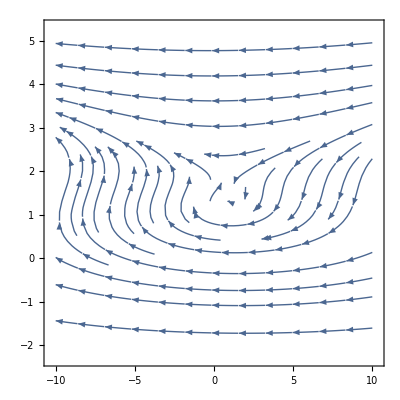

```mathematica
StreamPlot[{F1[s,i],F2[s,i]},{s,-10,10},{i,-2,5}]
```

```mathematica
vp=VectorPlot[{F1[s,i],F2[s,i]},{s,-4,4},{i,-4,4},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{s,i},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}];
```

```mathematica
cp=ContourPlot[{F1[s,i]==0,F2[s,i]==0},{s,-4,4},{i,-4,4}];
```

```mathematica
ptRules=NSolve[{F1[s,i]==0,F2[s,i]==0},{s,i}];
```

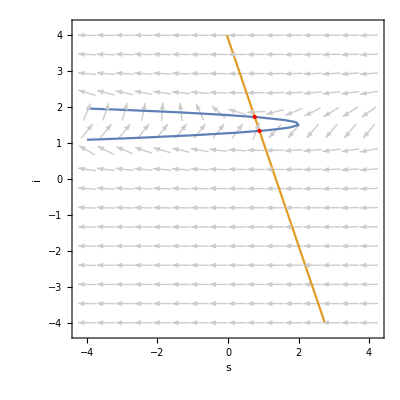

```mathematica
Show[vp,cp,Graphics[{Red,PointSize[Large],Tooltip[Point[{s,i}],Round[{s,i},.2]]/.ptRules}]]
```